```mathematica
coordinates=Table[(Get["gamess.out/opt."<>ToString[i]<>".m"];#[[3]]&/@molecule),{i,11}];
ct=Transpose[coordinates];
```

```mathematica
coordinates=Table[(Get["gamess.out/opv5-tb."<>ToString[i]<>".m"];#[[3]]&/@molecule),{i,2}];
ct=Transpose[coordinates];
```

```mathematica
(#[[1]]-ct[[1,1,1]])&/@ct[[1]]
```

{0.,-0.00418713,0.00930701,0.0161034,0.0235466,0.0343494,0.032531,0.0418812,0.0436892,0.0449546,0.049079}

```mathematica
diffplot[cs_]:=ListPlot[{(#[[1]]-cs[[1,1]])&/@cs,
(#[[2]]-cs[[1,2]])&/@cs,
(#[[3]]-cs[[1,3]])&/@cs},PlotRange->All,Joined->True,Axes->{False,True}]

diffplot[cs_,i_]:=ListPlot[(#[[i]]-cs[[1,i]])&/@cs,PlotRange->All,Joined->True,Axes->{False,True}]
```

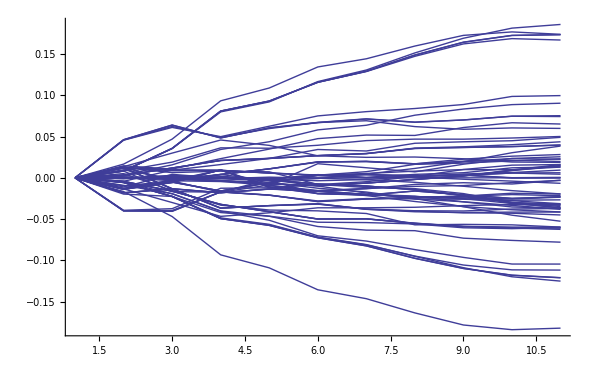

```mathematica
Show[diffplot[#,1]&/@ct]
```

```mathematica
diffplots=diffplot/@ct;
```

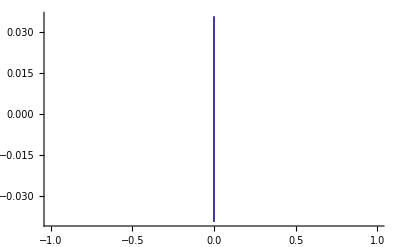

```mathematica
Show[diffplots]
```

```mathematica
ct[[2]]
```

{{-14.8157,-1.53401,0.0105826},{-14.802,-1.52823,0.0079088}}